## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.01;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataG=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/11/tables/g.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataG//TableForm
```

№линии | градусы | \lambda | 
23. | 1872. | 5400. | 5.
22. | 2130. | 5828. | 5.
21. | 2146. | 5885. | 5.
20. | 2174. | 5944. | 5.
19. | 2192. | 5975. | 5.
18. | 2218. | 6030. | 5.
17. | 2235. | 6074. | 5.
16. | 2248. | 6096. | 5.
15. | 2266. | 6143. | 5.
14. | 2274. | 6163. | 5.
13. | 2298. | 6217. | 5.
12. | 2318. | 6266. | 5.
11. | 2334. | 6304. | 5.
10. | 2346. | 6334. | 5.
9. | 2363. | 6382. | 5.
8. | 2372. | 6402. | 5.
7. | 2412. | 6506. | 5.
6. | 2418. | 6532. | 5.
5. | 2440. | 6598. | 5.
4. | 2466. | 6678. | 5.
3. | 2478. | 6717. | 5.
2. | 2544. | 6929. | 5.
1. | 2575. | 7032. | 5.

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFit=data⟦2;;,{1,4}⟧;
fit=LinearModelFit[forFit,{1,x},x]
fit@"ParameterTable"
Plot[fit["Function"]@x, {x, 0, 32}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

```mathematica
Show[ListPlot[data⟦2;;,{4,3}⟧,
GridLines->{grids@2.5,grids@2.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
Ticks->{myTicY, myTicY}, 
PlotRange->{{0,34},{0,34}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

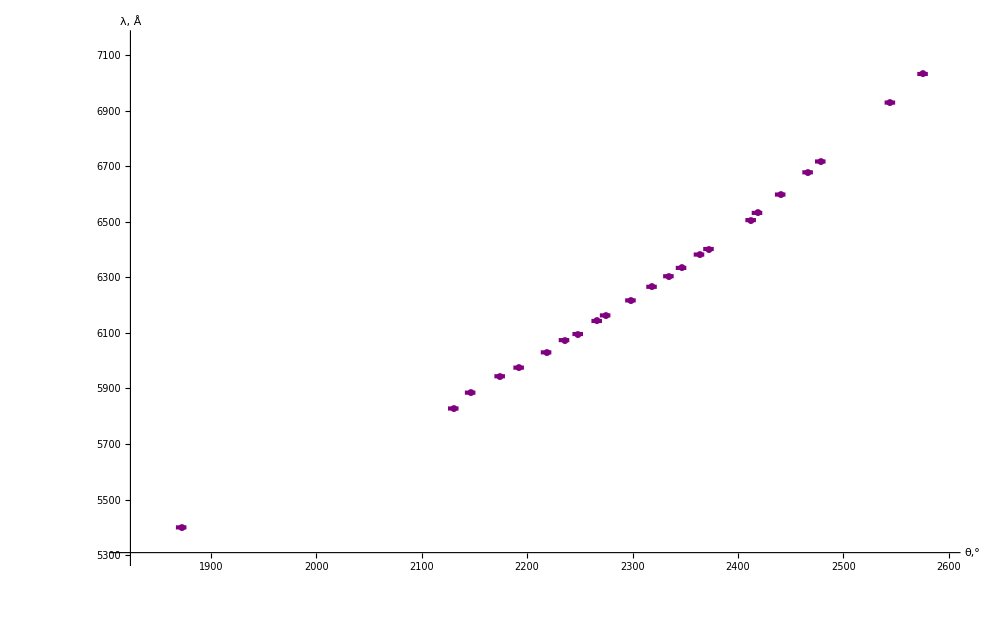

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataG⟦2;;,{2,3,4,1}⟧,
GridLines->{grids@25,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"θ,°","λ, Å"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
(*vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),*)
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{Automatic,myTicY},
PlotRange->{{1820,2595},{5300,7150}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataIbig=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/11/tables/Ibig.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataIbig//TableForm
```

№ | V | I |  |  | 
1. | 6.797 | 0.586 | 0.2 | 0.765506 | 0.0476551
2. | 6.223 | 0.582 | 0.2 | 0.762889 | 0.0476289
3. | 5.782 | 0.577 | 0.2 | 0.759605 | 0.0475961
4. | 5.235 | 0.571 | 0.2 | 0.755645 | 0.0475565
5. | 4.701 | 0.563 | 0.2 | 0.750333 | 0.0475033
6. | 4.2 | 0.556 | 0.2 | 0.745654 | 0.0474565
7. | 3.64 | 0.545 | 0.2 | 0.738241 | 0.0473824
8. | 3.06 | 0.531 | 0.2 | 0.728697 | 0.047287
9. | 2.565 | 0.515 | 0.2 | 0.717635 | 0.0471764
10. | 2.1 | 0.489 | 0.2 | 0.699285 | 0.0469929
11. | 1.43 | 0.44 | 0.2 | 0.663325 | 0.0466332
12. | 0.9 | 0.34 | 0.2 | 0.583095 | 0.045831
13. | 0.41 | 0.173 | 0.2 | 0.415933 | 0.0441593
14. | 0.02 | 0.069 | 0.2 | 0.262679 | 0.0426268
15. | -0.02 | 0.057 | 0.2 | 0.238747 | 0.0423875
16. | -0.18 | 0.034 | 0.2 | 0.184391 | 0.0418439
17. | -0.3 | 0.015 | 0.2 | 0.122474 | 0.0412247
18. | -1.125 | -0.005 | 0.2 | -0.0707107 | 0.0414142
19. | -1.75 | -0.005 | 0.2 | -0.0707107 | 0.0414142
20. | -3.04 | -0.005 | 0.2 | -0.0707107 | 0.0414142

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
dataIbigfit=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/11/tables/fitbig.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataIbigfit//TableForm
```

№ |  |  |  |  | 
12. | 0.9 | 0.34 | 0.2 | 0.583095 | 0.0408167
13. | 0.41 | 0.173 | 0.2 | 0.415933 | 0.0291153
14. | 0.02 | 0.069 | 0.2 | 0.262679 | 0.0183875
15. | -0.02 | 0.057 | 0.2 | 0.238747 | 0.0167123
16. | -0.18 | 0.034 | 0.2 | 0.184391 | 0.0129074
17. | -0.3 | 0.015 | 0.2 | 0.122474 | 0.00857321
18. | -1.125 | -0.005 | 0.2 | -0.0707107 | -0.00494975

FittedModel[0.262023+0.330687 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.262023 | 0.0116165 | 22.5561 | 3.18334×10^-6
x | 0.330687 | 0.0199771 | 16.5533 | 0.000014691

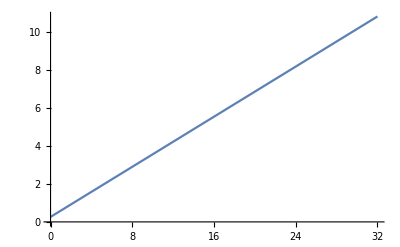

```mathematica
forFitBig=dataIbigfit⟦2;;,{2,5}⟧;
fitBig=LinearModelFit[forFitBig,{1,x},x]
fitBig@"ParameterTable"
Plot[fitBig["Function"]@x, {x, 0, 32}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,1}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

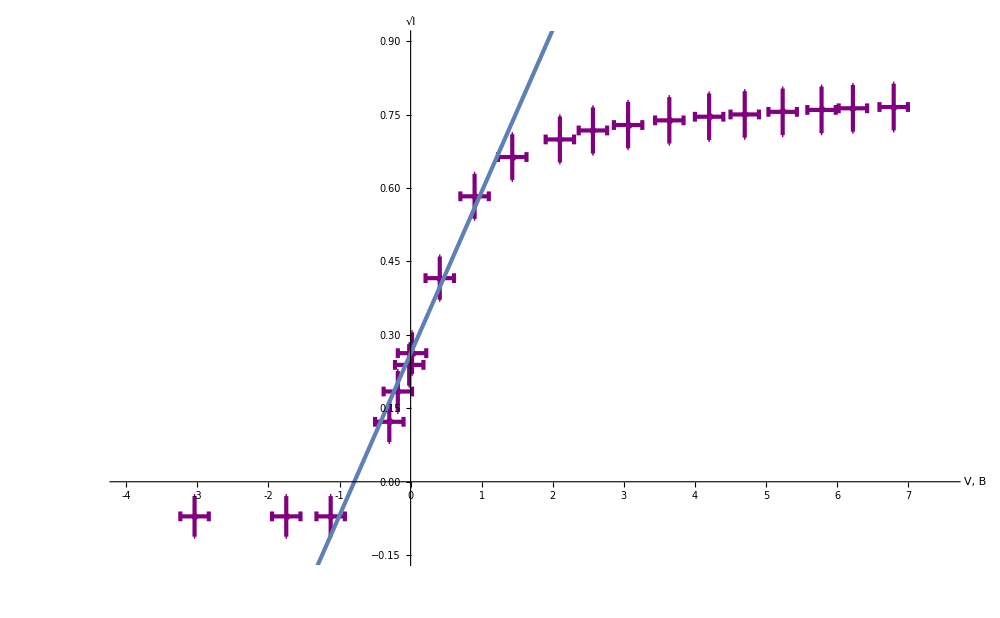

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataIbig⟦2;;,{2,5,4,6}⟧,
GridLines->{grids@0.25,grids@0.1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"V, В","√I"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{myTicX,Automatic},
PlotRange->{{-4,7.5},{-0.15,0.9}}], 
Plot[fitBig["Function"]@x,{x,-10,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataI2235=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/11/tables/I2235.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataI2235//TableForm
```

№ | V | I |  |  | 
1. | 0.939 | 0.328 | 0.15 | 0.572713 | 0.0407271
2. | 0.645 | 0.248 | 0.15 | 0.497996 | 0.03998
3. | 0.24 | 0.119 | 0.15 | 0.344964 | 0.0384496
4. | 0.399 | 0.178 | 0.15 | 0.4219 | 0.039219
5. | 0.695 | 0.282 | 0.15 | 0.531037 | 0.0403104
6. | 0.077 | 0.081 | 0.15 | 0.284605 | 0.037846
7. | 0.02 | 0.069 | 0.15 | 0.262679 | 0.0376268
8. | -0.835 | 0.003 | 0.15 | 0.0547723 | 0.0355477

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.287127+0.309012 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.287127 | 0.0099297 | 28.916 | 1.13324×10^-7
x | 0.309012 | 0.0170887 | 18.0828 | 1.84065×10^-6

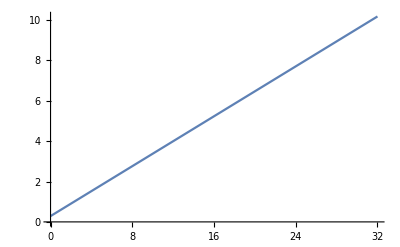

```mathematica
forFit2235=dataI2235⟦2;;,{2,5}⟧;
fit2235=LinearModelFit[forFit2235,{1,x},x]
fit2235@"ParameterTable"
Plot[fit2235["Function"]@x, {x, 0, 32}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX2235[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.25}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

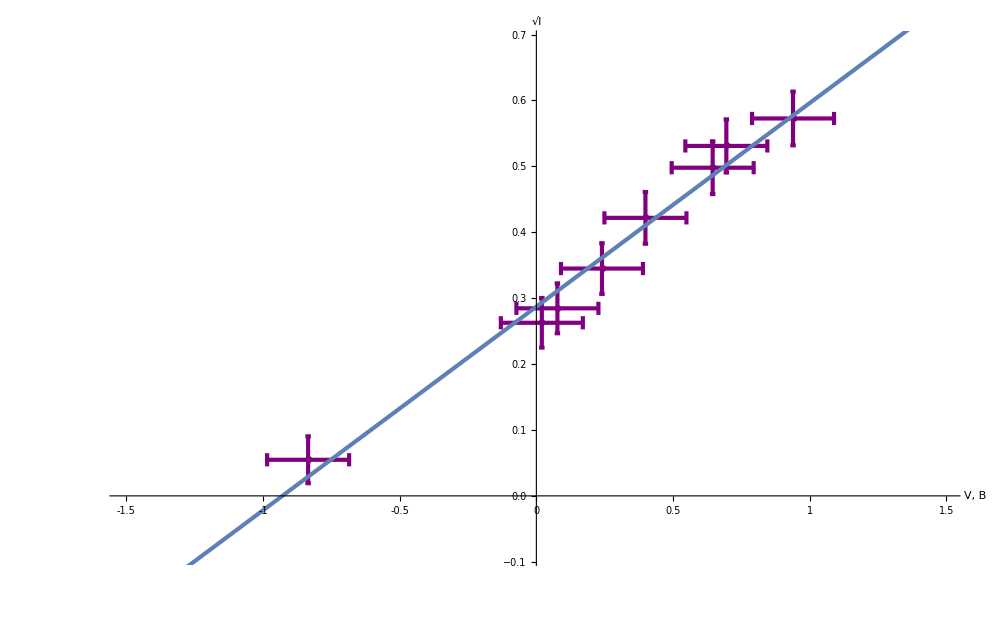

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataI2235⟦2;;,{2,5,4,6}⟧,
GridLines->{grids@0.1,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"V, В","√I"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{myTicX2235,Automatic},
PlotRange->{{-1.5,1.49},{-0.09,0.69}}], 
Plot[fit2235["Function"]@x,{x,-35,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```